## NMR Relaxation of 1H of water molecules

### Reading the data files obtained from the MD simulations' trajectories:

```mathematica
factorT1 = 100; (* time scale intermolecular correlation functions in fs*)
factorT2 = 10; (* time scale intramolecular correlation functions in fs*)
listRelaxDipInter=Import["/home/ccalero/Documents/0_RECERCA/Fase_plastica_aigua_NMR_relaxation/Analisi/LIQUID/Relaxation_dipolar_intermolecular_npt_all_100.dat"];
coef00DipInter=Table[{listRelaxDipInter[[n+1,1]],listRelaxDipInter[[n+1,2]]},{n,1,Length[listRelaxDipInter]-2}];
coef11DipInter=Table[{listRelaxDipInter[[n+1,1]],listRelaxDipInter[[n+1,3]]},{n,1,Length[listRelaxDipInter]-2}];
coef22DipInter=Table[{listRelaxDipInter[[n+1,1]],listRelaxDipInter[[n+1,5]]},{n,1,Length[listRelaxDipInter]-2}];

listRelaxDipIntra=Import["/home/ccalero/Documents/0_RECERCA/Fase_plastica_aigua_NMR_relaxation/Analisi/LIQUID/Relaxation_dipolar_intramolecular_npt_all_10.dat"];
coef00DipIntra=Table[{listRelaxDipIntra[[n+1,1]],listRelaxDipIntra[[n+1,2]]},{n,1,Length[listRelaxDipIntra]-2}];
coef11DipIntra=Table[{listRelaxDipIntra[[n+1,1]],listRelaxDipIntra[[n+1,3]]},{n,1,Length[listRelaxDipIntra]-2}];
coef22DipIntra=Table[{listRelaxDipIntra[[n+1,1]],listRelaxDipIntra[[n+1,5]]},{n,1,Length[listRelaxDipIntra]-2}];
```

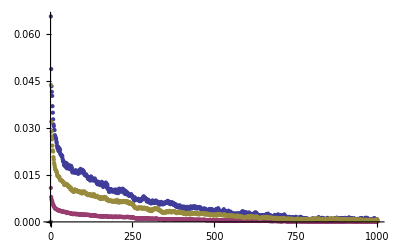

```mathematica
ListPlot[{coef00DipInter, coef11DipInter, coef22DipInter}, PlotRange -> All]
```

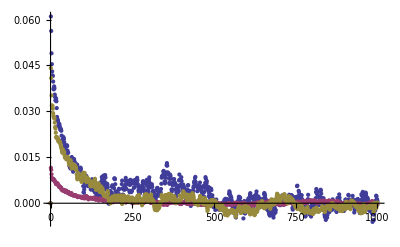

```mathematica
ListPlot[{coef00DipIntra,coef11DipIntra,coef22DipIntra},PlotRange->All]
```

### Obtaining interpolating functions and/or fits of the data:

```mathematica
Interpolcoef00DipInter = Interpolation[coef00DipInter];
Interpolcoef11DipInter = Interpolation[coef11DipInter];
Interpolcoef22DipInter = Interpolation[coef22DipInter];

Interpolcoef00DipIntra = Interpolation[coef00DipIntra];
Interpolcoef11DipIntra = Interpolation[coef11DipIntra];
Interpolcoef22DipIntra = Interpolation[coef22DipIntra];
```

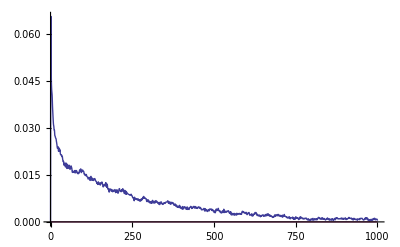

```mathematica
Plot[{Interpolcoef00DipInter[x],0},{x,0, 1000}, PlotRange-> All]
```

#### Intermolecular contribution

{a→0.020909,b→0.00359168,c→0.0204417,d→0.0618344}

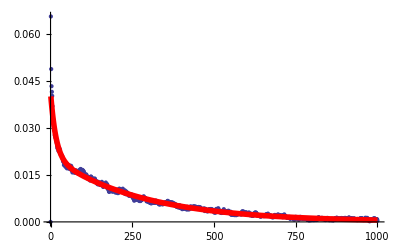

```mathematica
resfit00DipInter = FindFit[coef00DipInter,{ a*Exp[-b*x]+c*Exp[-d*x],a>0, b>0, c>0, d>0},{{a,0.2},b,c,d},x]
a00DipInter = a /. resfit00DipInter[[1]]; b00DipInter = b /. resfit00DipInter[[2]];c00DipInter = c /. resfit00DipInter[[3]];d00DipInter = d /. resfit00DipInter[[4]];
Fitcoef00DipInter[x_] = a00DipInter*Exp[-b00DipInter*x]+ c00DipInter*Exp[-d00DipInter*x];
Show[ListPlot[coef00DipInter, PlotRange-> All],Plot[Fitcoef00DipInter[x],{x,1,1000}, PlotRange-> {0,1000},PlotStyle->{Red, Thickness-> 0.01}]]
```

{a→0.00326756,b→0.0036475,c→0.00349448,d→0.0578977}

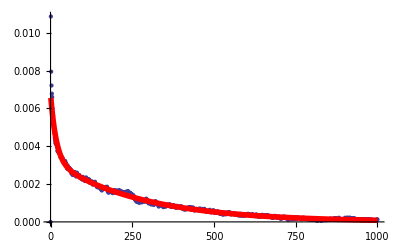

```mathematica
resfit11DipInter = FindFit[coef11DipInter,{ a*Exp[-b*x]+c*Exp[-d*x],a>0, b>0, c>0, d<1},{{a,0.01},b,c,{d,0.1}},x]
a11DipInter = a /. resfit11DipInter[[1]]; b11DipInter = b /. resfit11DipInter[[2]];
c11DipInter = c /. resfit11DipInter[[3]];d11DipInter = d /. resfit11DipInter[[4]];
Fitcoef11DipInter[x_] = a11DipInter*Exp[-b11DipInter*x]+ c11DipInter*Exp[-d11DipInter*x];
Show[ListPlot[coef11DipInter, PlotRange-> All],Plot[Fitcoef11DipInter[x],{x,1,1000}, PlotRange-> {0,1000},PlotStyle->{Red, Thickness-> 0.01}]]
```

{a→0.0130103,b→0.00354161,c→0.0144858,d→0.0646745}

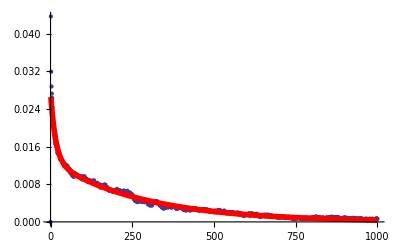

```mathematica
resfit22DipInter = FindFit[coef22DipInter, { a*Exp[-b*x]+c*Exp[-d*x],a>0, b>0, c>0, d<1},{{a,0.01},b,c,{d,0.02}},x]
a22DipInter = a /. resfit22DipInter[[1]]; b22DipInter = b /. resfit22DipInter[[2]];
c22DipInter = c /. resfit22DipInter[[3]];d22DipInter = d /. resfit22DipInter[[4]];
Fitcoef22DipInter[x_] = a22DipInter*Exp[-b22DipInter*x]+ c22DipInter*Exp[-d22DipInter*x];
Show[ListPlot[coef22DipInter, PlotRange-> All],Plot[Fitcoef22DipInter[x],{x,1,1000}, PlotRange-> {0,1000},PlotStyle->{Red, Thickness-> 0.01}]]
```

#### Intramolecular contribution

{a→-0.0421882,b→830.019,c→0.0421882,d→0.0153943}

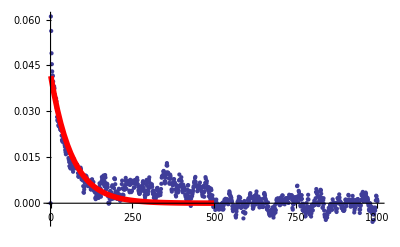

```mathematica
resfit00DipIntra = FindFit[coef00DipIntra,  a*Exp[-b*x]+c*Exp[-d*x],{{a,0.01},b,c,{d,0.02}},x]
a00DipIntra = a /. resfit00DipIntra[[1]]; b00DipIntra = b /. resfit00DipIntra[[2]];
c00DipIntra = c /. resfit00DipIntra[[3]];d00DipIntra = d /. resfit00DipIntra[[4]];
Fitcoef00DipIntra[x_] = a00DipIntra*Exp[-b00DipIntra*x]+ c00DipIntra*Exp[-d00DipIntra*x];
Show[ListPlot[coef00DipIntra, PlotRange-> All],Plot[Fitcoef00DipIntra[x],{x,1,500}, PlotRange-> {0,500},PlotStyle->{Red, Thickness-> 0.01}]]
```

{a→-0.00845793,b→765.948,c→0.00845793,d→0.0144526}

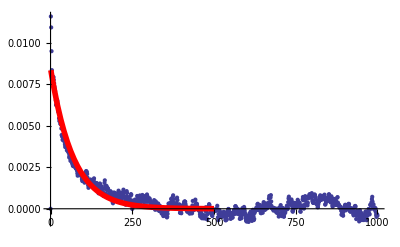

```mathematica
resfit11DipIntra = FindFit[coef11DipIntra, a*Exp[-b*x]+c*Exp[-d*x],{{a,0.01},b,c,{d,0.02}},x]
a11DipIntra = a /. resfit11DipIntra[[1]]; b11DipIntra = b /. resfit11DipIntra[[2]];
c11DipIntra = c /. resfit11DipIntra[[3]];d11DipIntra = d /. resfit11DipIntra[[4]];
Fitcoef11DipIntra[x_] = a11DipIntra*Exp[-b11DipIntra*x]+ c11DipIntra*Exp[-d11DipIntra*x];
Show[ListPlot[coef11DipIntra, PlotRange-> All],Plot[Fitcoef11DipIntra[x],{x,1,500}, PlotRange-> {0,500},PlotStyle->{Red, Thickness-> 0.01}]]
```

{a→-0.0316113,b→750.741,c→0.0316113,d→0.013936}

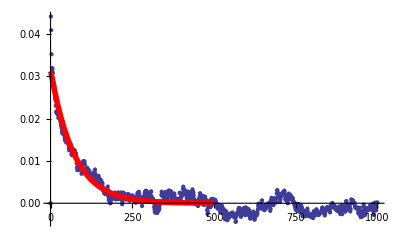

```mathematica
resfit22DipIntra = FindFit[coef22DipIntra, a*Exp[-b*x]+c*Exp[-d*x],{{a,0.01},b,c,{d,0.02}},x]
a22DipIntra = a /. resfit22DipIntra[[1]]; b22DipIntra = b /. resfit22DipIntra[[2]];
c22DipIntra = c /. resfit22DipIntra[[3]];d22DipIntra = d /. resfit22DipIntra[[4]];
Fitcoef22DipIntra[x_] = a22DipIntra*Exp[-b22DipIntra*x]+ c22DipIntra*Exp[-d22DipIntra*x];
Show[ListPlot[coef22DipIntra, PlotRange-> All],Plot[Fitcoef22DipIntra[x],{x,1,500}, PlotRange-> {0,500},PlotStyle->{Red, Thickness-> 0.01}]]
```

### Calculation of Spectral functions

```mathematica
ω1 = 267.513*10^-9*factorT1;ω2 = 267.513*10^-9*factorT2; (* for H = 1T, in femtoseconds^-1 *)
```

```mathematica
J00DipInter = ∫_0^∞ Fitcoef00DipInter[x]Cos[ω1*x]ⅆx
J11DipInter = ∫_0^∞ Fitcoef11DipInter[x]Cos[ω1*x]ⅆx
J22DipInter = ∫_0^∞ Fitcoef22DipInter[x]Cos[ω1*x]ⅆx
```

6.15178

0.956143

3.89732

```mathematica
J00DipInter0 = ∫_0^∞ Fitcoef00DipInter[x]ⅆx
J11DipInter0 = ∫_0^∞ Fitcoef11DipInter[x]ⅆx
J22DipInter0 = ∫_0^∞ Fitcoef22DipInter[x]ⅆx
```

6.1521

0.956191

3.89753

```mathematica
J00DipIntra = ∫_0^∞ Fitcoef00DipIntra[x]Cos[ω2*x]ⅆx
J11DipIntra = ∫_0^∞ Fitcoef11DipIntra[x]Cos[ω2*x]ⅆx
J22DipIntra = ∫_0^∞ Fitcoef22DipIntra[x]Cos[ω2*x]ⅆx
```

2.74046

0.585208

2.26827

```mathematica
J00DipIntra0 = ∫_0^∞ Fitcoef00DipIntra[x]ⅆx
J11DipIntra0 = ∫_0^∞ Fitcoef11DipIntra[x]ⅆx
J22DipIntra0 = ∫_0^∞ Fitcoef22DipIntra[x]ⅆx
```

2.74046

0.585208

2.26827

### Calculation of relaxation times T1, T2 (cgs)

```mathematica
h = 1.05*10^-27;γ = 267.513*10^2; factorT1 =100; factorT2 =10;
```

```mathematica
Γ1=9/8 γ^4 h^2 2((J11DipInter0 + J22DipInter0)factorT1+(J11DipIntra0 + J22DipIntra0)factorT2)*10^(48-15)
T1 = 1/Γ1
```

0.652868

1.5317

```mathematica
Γ2=γ^4 h^2 2 3/4((3/8 J00DipInter0+15/4 J11DipInter0 + 3/8 J22DipInter0)factorT1+ (3/8 J00DipIntra0+15/4 J11DipIntra0+ 3/8 J22DipIntra0)factorT2)*10^(48-15)
1/Γ2
```

0.657357

1.52124

### Calculation of relaxation times T1, T2 (SI)

```mathematica
h = 1.05*10^-34; μ= 4π*10^-7;γ = 267.513*10^6;
```

```mathematica
Γ1=9/8(μ/(4π))^2 γ^4 h^2 2((J11DipInter0 + J22DipInter0)*factorT1+(J11DipIntra0 + J22DipIntra0)*factorT2)*10^(60-15)
T1 = 1/Γ1
```

0.652868

1.5317

```mathematica
Γ2= 3/4(μ/(4π))^2 γ^4 h^2 2((3/8 J00DipInter0+15/4 J11DipInter0 + 3/8 J22DipInter0)*factorT1+ (3/8 J00DipIntra0+15/4 J11DipIntra0 + 3/8 J22DipIntra0)*factorT2)*10^(60-15)
T2=1/Γ2
```

0.657357

1.52124

### Ratio of intermolecular over intramolecular contributions to T1, T2

```mathematica
R1= (J11DipInter0+J22DipInter0) factorT1/((J11DipIntra0+J22DipIntra0)factorT2)
R2= (3/8 J00DipInter0+15/4 J11DipInter0+3/8 J22DipInter0) factorT1/((3/8 J00DipIntra0+15/4 J11DipIntra0+3/8 J22DipIntra0) factorT2)
```

17.0098

18.0572